# Narrow type interactions

```mathematica
Subscript[V, smooth][x_, b_,xc_]:=b(xc-x)^2
```

```mathematica
Subscript[V, mod][θ_,a_,θ0_]:=1-a(θ-θ0)^2
```

```mathematica
Subscript[V, angmod][θ_, θ0_, Δ_, Δc_,a_, b_]:=
Piecewise[{
{Subscript[V, mod][θ, a, θ0],θ0-Δ<θ<θ0+Δ},
{Subscript[V, smooth][θ, b, θ0- Δc],θ0-Δc<θ<θ0-Δ},
{Subscript[V, smooth][θ, b, θ0+ Δc],θ0+Δ<θ<θ0+Δc}}
]
```

```mathematica
nt0 = With[
{θ0 = 0,Δ=0.7 , Δc=3.10559,a=0.46, b=0.133855},
Subscript[V, angmod][θ, θ0, Δ, Δc,a, b]];
nt1=With[
{θ0 = 0,Δ=0.2555, Δc=1.304631441617743,a=3, b=0.7306043547966398},
Subscript[V, angmod][θ, θ0, Δ, Δc,a, b]];
nt2 = With[
{θ0 = 0,Δ=0.2555 , Δc=0.782779,a=5, b=2.42282},
Subscript[V, angmod][θ, θ0, Δ, Δc,a, b]];
nt3 = With[
{θ0 = 0,Δ=0.17555 , Δc=0.4381832920710734,a=13, b=8.68949241736805},
Subscript[V, angmod][θ, θ0, Δ, Δc,a, b]];
nt4 =With[
{θ0 = 0,Δ=0.17555 , Δc=0.322741,a=17.65, b=21.0506},
Subscript[V, angmod][θ, θ0, Δ, Δc,a, b]];
```

### Finding the width of the potentials

```mathematica
Grid[{
{"nt0","nt1","nt2","nt3","nt4"},
EuclideanDistance@@SolveValues[#==0.5,θ]&/@{nt0,nt1,nt2,nt3,nt4}
},Frame->All]
```

nt0 | nt1 | nt2 | nt3 | nt4
2.34575 | 0.954736 | 0.656996 | 0.396613 | 0.336622

### Plot

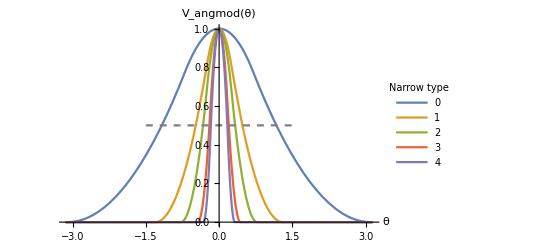

```mathematica
plot =  Show[
Plot[{
nt0,nt1,nt2,nt3,nt4
},{θ,-π,π},
PlotLegends->LineLegend[{0,1,2,3,4},LegendLabel->"Narrow type"],
AxesLabel->Automatic, 
PlotLabel->"V_angmod(θ)"
],
Plot[0.5, {θ,-1.5,1.5},PlotStyle->{Dashed,Gray, Thin}]
]
```

```mathematica
Export["/home/joakim/repo/DPhil_thesis/figures/patchysim/nts.eps",plot,"EPS"]
```

/home/joakim/repo/DPhil_thesis/figures/patchysim/nts.eps

## Playing around with the constants

```mathematica
Manipulate[Plot[Subscript[V, angmod][θ, θ0, Δ, Δc,a, b],{θ,-π,π}, PlotRange->Full], 
{θ0,-1,1},
{Δ,0.17,0.7},
{Δc,0.3,3.2},
{a,0.46,17.65},
{b,0.134,21.05}
]
```